This notebook finds parameters to best fit the theoretical model of a DC motor to collected data.

Define constants

```mathematica
(* The maximum voltage of the motor. *)
motorVoltage=24;
```

```mathematica
(* The radius of the timing pulley on the axle of the motor in m. Multiplying an angle change by this value gives the distance the cart moves. *)
timingPulleyRadius=0.00965;
```

Import the data

```mathematica
dataDirectory=FileNameJoin[{NotebookDirectory[],"..","data"}];
```

```mathematica
dataPaths=FileNames["*.csv",dataDirectory];
```

```mathematica
(* The columns are index, time (in us), and angle (in radians) *)
data=Import[#,"csv"]&/@dataPaths;
```

Calculate the PWM duty cycles and voltages from the file names

```mathematica
dataFilenames=FileNameSplit[#][[-1]]&/@dataPaths;
```

```mathematica
(* Moving to the left is considered positive *)
```

```mathematica
pwms=If[StringPart[#,1]=="l",1,-1]FromDigits[StringJoin[StringPart[#,{2,3}]]]&/@dataFilenames;
```

```mathematica
voltages=N[(# /255)motorVoltage]&/@pwms;
```

Drop the index column, convert time to seconds, add voltage, and convert angle to cart position

```mathematica
(* Time (in s), voltage (in V), position (in m) *)
positions=MapIndexed[
Module[
{i=#2[[1]],voltage=voltages[[#2[[1]]]]},
{N[(#[[2]]-data[[i,1,2]])/1*^6],voltage,timingPulleyRadius#[[3]]}&/@#1
]&,
data
];
```

Calculate velocities

```mathematica
(* Time (in s), voltage (in V), velocity (in m/s) *)
velocities={#[[2,1]],#[[2,2]],(#[[2,3]]-#[[1,3]])/(#[[2,1]]-#[[1,1]])}&/@Partition[#,2,1]&/@positions;
```

Plot velocities

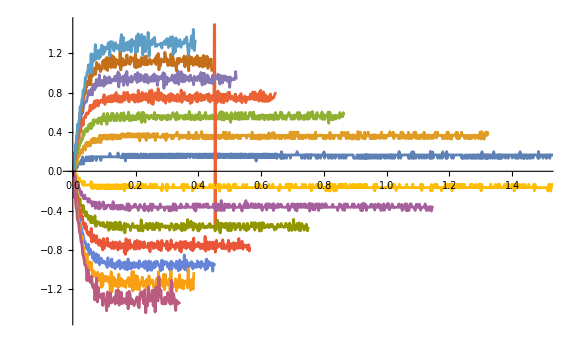

```mathematica
velocityPlot=ListLinePlot[{#[[1]],#[[3]]}&/@#&/@velocities,ImageSize->Large,PlotRange->{{0,1.5},{-1.5,1.5}}]
```

Fit the time-dependent equation to the data

```mathematica
parameters=FindFit[Join@@velocities,a v(1-E^(-b t)),{a,b},{t,v}]
```

{a→0.196987,b→33.0202}

Plot the fitted model

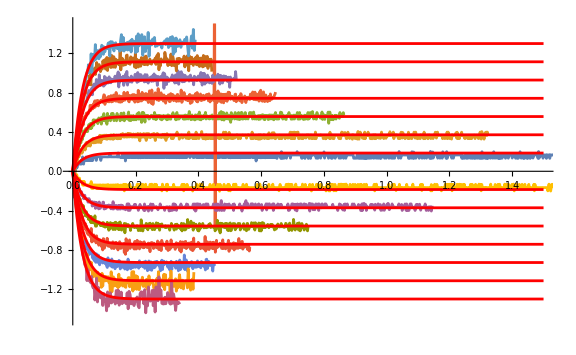

```mathematica
Show[
velocityPlot,
Plot[(a#(1-E^(-b t))/.parameters)&/@voltages,{t,0,1.5},PlotStyle->Red]
]
```

Calculate the time-independent parameters

```mathematica
c=a b/.parameters
```

6.50454

```mathematica
d=-b/.parameters
```

-33.0202

Using these constants we can “integrate” the time-independent equation for the cart’s acceleration to get its velocity and plot this with the collected data.

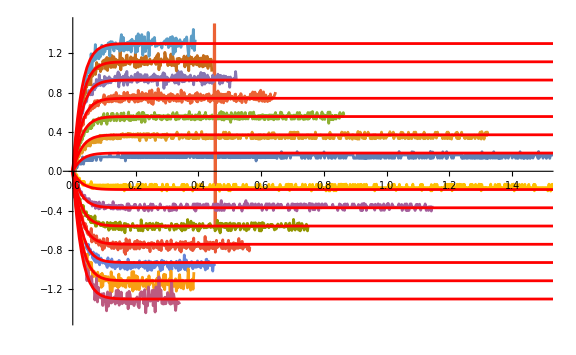

```mathematica
plot=Show[
velocityPlot,
ListLinePlot[
MapIndexed[
Module[
{i=#2[[1]],voltage=#1},
FoldList[
{#1[[1]]+#2,#1[[2]]+(c voltage+d#1[[2]])#2}&,
{0,0},
Range[0,1,0.001]
]
]&,
voltages
],
PlotStyle->Red
]
]
```

Uncomment to export an image of the plot

```mathematica
(*Export[
FileNameJoin[{NotebookDirectory[],"motor.png"}],
plot
];*)
```